# Demonstrating well - known solutions of the Burgers equation

```mathematica
{brown,green,beige,blue}=RGBColor/@{"#d80125","#6ed855","#fbe933","#165e83"}
```

{RGBColor[0.8470588235294118, 0.00392156862745098, 0.1450980392156863],RGBColor[0.43137254901960786, 0.8470588235294118, 0.3333333333333333],RGBColor[0.984313725490196, 0.9137254901960784, 0.2],RGBColor[0.08627450980392157, 0.3686274509803922, 0.5137254901960784]}

```mathematica
nu=0.1 (*heat conductivity*);
SimTime=3.;
BoxSize=15.;
{tMin,tMax}={0,SimTime} (*time*);
{xMin,xMax}={-BoxSize/2.,BoxSize/2.} (*x coordinate*);
{xMinP,xMaxP}={-BoxSize/4.,BoxSize/4.} (*x coordinate for plot*);
xgr=376;dx=BoxSize/(xgr-1);
tgr=9000;dt=SimTime/(tgr-1);
nu*dt/dx^2<=1/2 (*for numerical stability*)
```

True

```mathematica
IC1[x_]:=Exp[-Min[x,0]/(2.*nu)](*Shock1*);
IC2[x_]:=Exp[-Min[x+1,Max[0.75+0.5*x-0.25*x^2,0.5*x+0.5],1]/(2.*nu)] (*Shock2*);
IC3[x_]:=Exp[-Max[0,Min[0.25+0.5*x+0.25*x^2,0.5*x+0.5],x]/(2.*nu)] (*Dilution fan*);
```

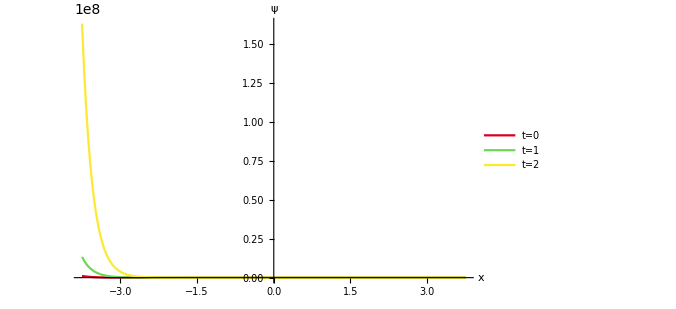

./Desktop/projects/QC_Burgers/code_revise2/phi260306_dilution.pdf

```mathematica
xGrid=Range[xMin,xMax,dx];
phi0={};
For[i=1,i<=xgr,i++,AppendTo[phi0,IC2[xGrid[[i]]]]];
phi=phi0;
results={phi};

For[t=1,t<=tgr-1,t++,phiNew=phi;
For[i=2,i<=xgr-1,i++,phiNew[[i]]=phi[[i]]+nu*dt/dx^2*(phi[[i-1]]-2*phi[[i]]+phi[[i+1]]);];
(* phiNew[[1]]=phi[[1]]+nu*dt/dx^2*(phi[[xgr-1]]-2*phi[[1]]+phi[[2]]) (*PBC*);*)
(* phiNew[[xgr]]=phiNew[[1]](*PBC*);*)
phiNew[[1]]=phi[[1]]+nu*dt/dx^2*(phi[[1]]-2*phi[[1]]+phi[[2]]) (*Neumann*);phiNew[[xgr]]=phiNew[[xgr-1]](*Neumann*);
phi=phiNew;
AppendTo[results,phi];];

graph2=ListLinePlot[{results[[1]][[xgr/4;;xgr*3/4]],results[[3000]][[xgr/4;;xgr*3/4]],results[[6000]][[xgr/4;;xgr*3/4]]},DataRange->{xMinP,xMaxP},PlotRange->All,PlotStyle->{brown,green,beige},BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},ImageSize->500,PlotLegends->Placed[LineLegend[{"t=0","t=1","t=2"}],{Right,Top}],AxesLabel->{"x","ψ"}];

Show[graph2]
Export["test_phi.pdf",%]
```

```mathematica
u0={};
(*AppendTo[u0,-(2.*nu/(2.*dx))*(results[[1]][[2]]-results[[1]][[xgr-1]])/results[[1]][[1]]] (*PBC*);*)
AppendTo[u0,-(2.*nu/(2.*dx))*(results[[1]][[2]]-results[[1]][[1]])/results[[1]][[1]]] (*Neumann*);
For[i=2,i<=xgr-1,i++,AppendTo[u0,-(2.*nu/(2.*dx))*(results[[1]][[i+1]]-results[[1]][[i-1]])/results[[1]][[i]]];];
(* AppendTo[u0,-(2.*nu/(2.*dx))*(results[[1]][[2]]-results[[1]][[xgr-1]])/results[[1]][[xgr]]] (*PBC*);*)
AppendTo[u0,-(2.*nu/(2.*dx))*(results[[1]][[xgr]]-results[[1]][[xgr-1]])/results[[1]][[xgr]]] (*Neumann*);
u=u0;
uresults={u};

For[t=1,t<=tgr,t++,uNew=u;(*uNew[[1]]=-(2.*nu/(2.*dx))*(results[[t]][[2]]-results[[t]][[xgr-1]])/results[[t]][[1]] (*PBC*);*)
uNew[[1]]=-(2.*nu/(2.*dx))*(results[[t]][[2]]-results[[t]][[1]])/results[[t]][[1]] (*Neumann*);
For[i=2,i<=xgr-1,i++,uNew[[i]]=-(2.*nu/(2.*dx))*(results[[t]][[i+1]]-results[[t]][[i-1]])/results[[t]][[i]];];
(*uNew[[xgr]]=-(2.*nu/(2.*dx))*(results[[t]][[2]]-results[[t]][[xgr-1]])/results[[t]][[xgr]] (*PBC*);*)uNew[[xgr]]=-(2.*nu/(2.*dx))*(results[[t]][[xgr]]-results[[t]][[xgr-1]])/results[[t]][[xgr]] (*Neumann*);
u=uNew;
AppendTo[uresults,u];]
```

```mathematica
graph3=ListLinePlot[{uresults[[1]][[xgr/4;;xgr*3/4]],uresults[[3000]][[xgr/4;;xgr*3/4]],uresults[[6000]][[xgr/4;;xgr*3/4]]},DataRange->{xMinP,xMaxP},PlotRange->All,ImageSize->500,PlotStyle->{brown,green,beige},PlotLegends->Placed[LineLegend[{"t=0","t=1","t=2"}],{Right,Top}],AxesLabel->{"x","u"},BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"}];
```

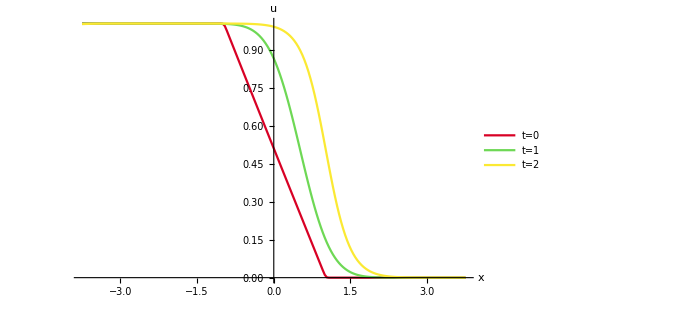

./Desktop/projects/QC_Burgers/code_revise2/Shock_260311.pdf

```mathematica
Show[graph3]
Export["Shock.pdf",%]
```